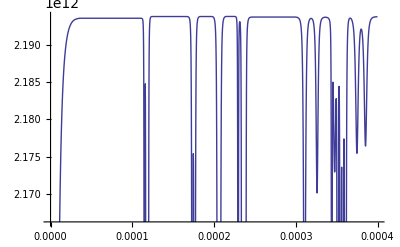

```mathematica
data = Import["toto.txt", "Table"];
dim = Dimensions[data];
time = data[[All,1]];
eKin = data[[All,2]];
ePot = data[[All,3]];
eTot = data[[All,4]];
eCoh = data[[All,5]];
msd = data[[All,6]];
P = data[[All,7]];
T = data[[All,8]];
debTemp = data[[All,9]];
Cv = data[[All,10]];

ListLinePlot[Table[{time[[i]],[[i]]},{i,dim[[1]]}]]
```